```mathematica
Quit[]
```

## Import astro

InterpolatingFunction[…]

1.79423×10^-9

0.

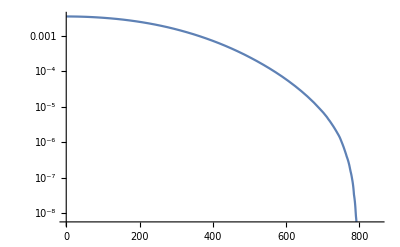

```mathematica
SetDirectory[NotebookDirectory[]];
Lgvmin=Import["../gvmin_round.dat"];
ResetDirectory[];
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[794]
fgvmin[795]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

Function[{qx,Ex},If[qx>L1a⟦-1⟧⟦1⟧||Ex>L1a⟦-1⟧⟦2⟧,0,F1a[qx,Ex]]]

Function[{qx,Ex},If[qx>L2a⟦-1⟧⟦1⟧||Ex>L2a⟦-1⟧⟦2⟧,0,F2a[qx,Ex]]]

Function[{qx,Ex},If[qx>L1t⟦-1⟧⟦1⟧||Ex>L1t⟦-1⟧⟦2⟧,0,F1t[qx,Ex]]]

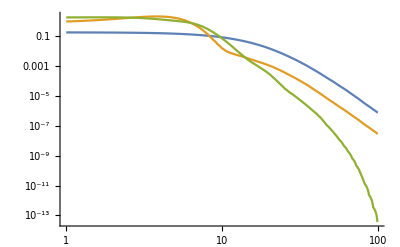

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../../Formfactor_planewave"];
(*set path to form factor files*)

L1a=Import["CH4_1a_grid.dat"];
L2a=Import["CH4_2a_grid.dat"];
L1t=Import["CH4_1tx_grid.dat"];
ResetDirectory[];

F1a=Interpolation[L1a,InterpolationOrder->1]
F2a=Interpolation[L2a,InterpolationOrder->1]
F1t=Interpolation[L1t,InterpolationOrder->1]

f1a=Function[{qx,Ex},If[qx>L1a[[-1]][[1]] ||Ex>L1a[[-1]][[2]],0,F1a[qx,Ex]]]
f2a=Function[{qx,Ex},If[qx>L2a[[-1]][[1]] ||Ex>L2a[[-1]][[2]],0,F2a[qx,Ex]]]
f1t=Function[{qx,Ex},If[qx>L1t[[-1]][[1]] ||Ex>L1t[[-1]][[2]],0,F1t[qx,Ex]]]

LogLogPlot[{f1a[qx,0.02],f2a[qx,0.02],f1t[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params1a=Association[
wnl->2,
Inl->290.8,
fionnl->f1a
];

Params2a=Association[
wnl->2,
Inl->22.9,
fionnl->f2a
];

Params1t=Association[
wnl->6,
Inl->13.6,
fionnl->f1t
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1t],InterpolationOrder->1];

Ftot[x_]:=fσ1a[x]+fσ2a[x]+fσ1t[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

```mathematica
TdREComponents[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1t],InterpolationOrder->1];

EikeV=0.001;
EfkeV=1.0;
steps=250;

T1=Table[{10^log10ErkeV,fσ1a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T2=Table[{10^log10ErkeV,fσ2a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T3=Table[{10^log10ErkeV,fσ1t[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

{T1,T2,T3}
]
```

### Calculate and Plot

```mathematica
ACH4=16.04;
MNGeV=ACH4 .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=Quiet[TdRETotal[30,MNGeV,σ1]];
TR300MeV=Quiet[TdRETotal[300,MNGeV,σ1]];
TR1000MeV=Quiet[TdRETotal[1000,MNGeV,σ1]];

Tcomponents30MeV=Quiet[TdREComponents[30,MNGeV,σ1]];
Tcomponents300MeV=Quiet[TdREComponents[300,MNGeV,σ1]];
Tcomponents1000MeV=Quiet[TdREComponents[1000,MNGeV,σ1]];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_CH4_30MeV.dat",TR30MeV]
Export["dRdE_CH4_300MeV.dat",TR300MeV]
Export["dRdE_CH4_1000MeV.dat",TR1000MeV]
ResetDirectory[];*)
```

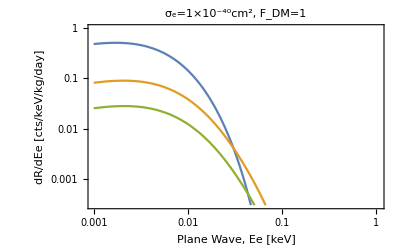

```mathematica
Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{10^-3 ,1070 10^-3},{3 10^-4,Automatic}}],Frame->True,FrameLabel->{"Plane Wave, Ee [keV]","dR/dEe [cts/keV/kg/day]"},PlotLabel->"σ_e="<>ToString[σ1]<>"×10^-40cm^2, F_DM=1"]
```

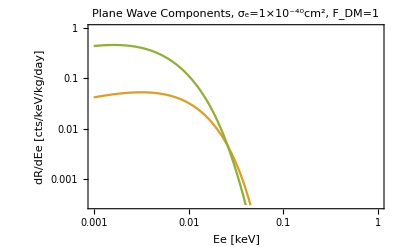

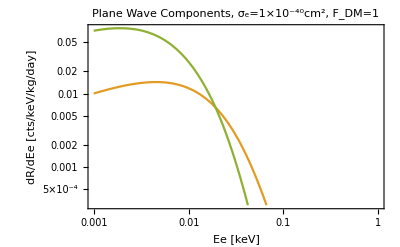

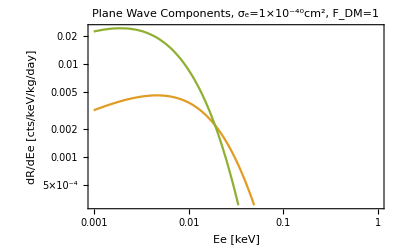

```mathematica
ListLogLogPlot[Tcomponents30MeV,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}},Frame->True,FrameLabel->{"Ee [keV]","dR/dEe [cts/keV/kg/day]"},PlotLabel->"Plane Wave Components, σ_e="<>ToString[σ1]<>"×10^-40cm^2, F_DM=1"]
ListLogLogPlot[Tcomponents300MeV,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}},Frame->True,FrameLabel->{"Ee [keV]","dR/dEe [cts/keV/kg/day]"},PlotLabel->"Plane Wave Components, σ_e="<>ToString[σ1]<>"×10^-40cm^2, F_DM=1"]
ListLogLogPlot[Tcomponents1000MeV,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}},Frame->True,FrameLabel->{"Ee [keV]","dR/dEe [cts/keV/kg/day]"},PlotLabel->"Plane Wave Components, σ_e="<>ToString[σ1]<>"×10^-40cm^2, F_DM=1"]
```

## Rate calculation: FDM = (alpha me / q)^2

σe37 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1t],InterpolationOrder->1];

Ftot[x_]:=fσ1a[x]+fσ2a[x]+fσ1t[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

```mathematica
TdREComponentslightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1t],InterpolationOrder->1];

EikeV=0.001;
EfkeV=1.0;
steps=250;

T1=Table[{10^log10ErkeV,fσ1a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T2=Table[{10^log10ErkeV,fσ2a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T3=Table[{10^log10ErkeV,fσ1t[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

{T1,T2,T3}
]
```

### Calculate and Plot

```mathematica
ACH4=16.04;
MNGeV=ACH4 .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=Quiet[TdRETotallightmed[30,MNGeV,σ1]];
TR300MeVlightmed=Quiet[TdRETotallightmed[300,MNGeV,σ1]];
TR1000MeVlightmed=Quiet[TdRETotallightmed[1000,MNGeV,σ1]];

Tcomponents30MeVlightmed=Quiet[TdREComponentslightmed[30,MNGeV,σ1]];
Tcomponents300MeVlightmed=Quiet[TdREComponentslightmed[300,MNGeV,σ1]];
Tcomponents1000MeVlightmed=Quiet[TdREComponentslightmed[1000,MNGeV,σ1]];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_CH4_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_CH4_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_CH4_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];*)
```

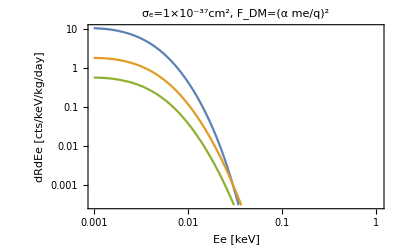

```mathematica
Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{10^-3,1070 10^-3},{3 10^-4,Automatic}}],Frame->True,FrameLabel->{"Ee [keV]","dRdEe [cts/keV/kg/day]"},PlotLabel->"σ_e="<>ToString[σ1]<>"×10^-37cm^2, F_DM=(α me/q)^2"]
```

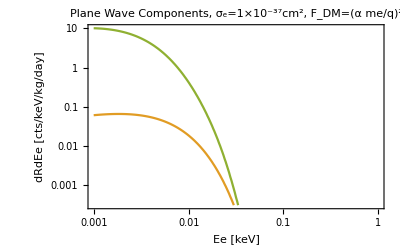

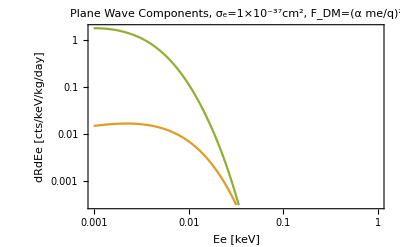

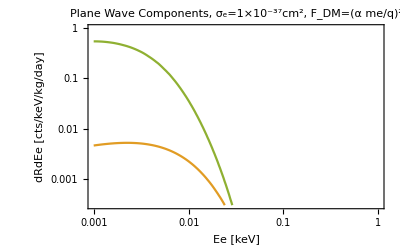

```mathematica
ListLogLogPlot[Tcomponents30MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}},Frame->True,FrameLabel->{"Ee [keV]","dRdEe [cts/keV/kg/day]"},PlotLabel->"Plane Wave Components, σ_e="<>ToString[σ1]<>"×10^-37cm^2, F_DM=(α me/q)^2"]
ListLogLogPlot[Tcomponents300MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}},Frame->True,FrameLabel->{"Ee [keV]","dRdEe [cts/keV/kg/day]"},PlotLabel->"Plane Wave Components, σ_e="<>ToString[σ1]<>"×10^-37cm^2, F_DM=(α me/q)^2"]
ListLogLogPlot[Tcomponents1000MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}},Frame->True,FrameLabel->{"Ee [keV]","dRdEe [cts/keV/kg/day]"},PlotLabel->"Plane Wave Components, σ_e="<>ToString[σ1]<>"×10^-37cm^2, F_DM=(α me/q)^2"]
```